Progress bar:

Start time: Tue 25 Apr 2023 14:39:00GMT+1

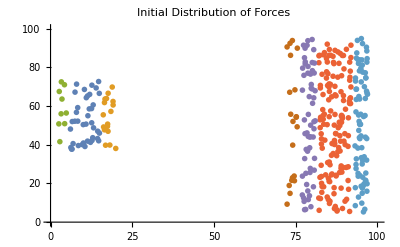

Army1 won

Calculations took 1.06112 min

```mathematica
(*Code created by Melania Mieczkowska, Artur Miralles and Joao Florido*)
Clear["`*"];

time1=Now; (* for checking how long the calculations take *)

dt = 0.02; (* time step *)
Nsteps=2500;  (* initial (max) number of steps in the simulation *)
ReachRange={2,3,1.5,10}; (* reach range order: Infantry, Lances, Cavalry, Bowmen *)
i=1; (* defined for the progress bar sake *)
Army1Start=900; (* at which points the armies start moving *)
Army2Start=400;
PlotRangee={{0,100},{0,100}}; (* predefining the plot range *)
loc1=GeoPosition[{39.60,-8.77}]; (* geo map *)
loc2=GeoPosition[{39.65,-8.77}];
loc3=GeoPosition[{39.55,-8.90}];
loc4=GeoPosition[{39.55,-8.90}];

v = 5 ; (* velocity of the troops *)
SlowingArea={{20,45},{25,75},{20,75},{25,45}}; (* area that slows soldiers down *)
DeadLocation={-1000,-1000}; (* location where we yeet dead soldiers *)
CavalryRoutIndicator=0; (* indicators for various events in the battle *)
BigRoutIndicator=0;
EndingRoutIndicator=0;
HealthIndicator=0;

Print["Progress bar:"]
ProgressIndicator[Dynamic[i/Nsteps]] (* adding progress bar for **glamm** *)
Print["Start time: ", Now]

(* number of soldiers in each unit type *)
NofInfantry1=40;(*40 - 4000 foot soldiers*)
NofLances1 =17; (*17 - 1700 lances*)
NofBowmen1=9;(*9 - 800 crossbowmen + 100 English longbowmen*)
InitialNofTroops1=NofInfantry1+NofLances1+NofBowmen1;
CurrentNofTroops1=InitialNofTroops1; (* this will change as soldiers die *)
NofTroops1={InitialNofTroops1}; (* list of numebr of soldiers, for plotting *)

NofInfantry2=150;(*150 - 15000 foot soldiers*)
NofLances2 =60; (*60 - 6000 lances*)
NofCavalry2=20;(*20 - 2000 French knights*)
NofBowmen2=80;(*80 - 8000 crossbowmen*)
InitialNofTroops2=NofInfantry2+NofLances2+NofCavalry2+NofBowmen2;
CurrentNofTroops2=InitialNofTroops2;
NofTroops2={InitialNofTroops2};

NofRout2=0; (* number of routed soldiers *)
BigRoutTime=Round[InitialNofTroops2-((InitialNofTroops2-NofCavalry2)*0.16+NofCavalry2/2)]; (* how many soldiers must be remaining in army2 for BigRout to start *)
EndingRoutTime=Round[InitialNofTroops2-((InitialNofTroops2-NofCavalry2)*0.32+NofCavalry2/2)];
(* how many soldiers must be remaining in army2 for EndingRout (Spaniards loosing) *)

(* troops types definition with initial placement *)
Army1Infantry=Table[{RandomReal[{6,15}],RandomReal[{37,73}]},NofInfantry1];
Army1Lances=Table[{RandomReal[{16,20}],RandomReal[{37,73}]},NofLances1];
Army1Bowmen=Table[{RandomReal[{2,5}],RandomReal[{37,73}]},NofBowmen1];

Army2Infantry=Table[{RandomReal[{82,92}],RandomReal[{5,95}]},NofInfantry2];
Army2Lances=Table[{RandomReal[{77,81}],RandomReal[{5,95}]},NofLances2];
Army2Cavalry=Table[{RandomReal[{72,76}],RandomReal[{5,95}]},NofCavalry2];
Army2Bowmen=Table[{RandomReal[{93,97}],RandomReal[{5,95}]},NofBowmen2];
Army2Rout={{∅}};

DeadSoldiers1 = {};
DeadSoldiers2={};

(* initial position of the armies *)
InitialArmy1Position = Join[Army1Infantry,Army1Lances,Army1Bowmen];
InitialArmy2Position= Join[Army2Infantry,Army2Lances,Army2Cavalry,Army2Bowmen];

(* defining arimes health, skill and morale parameters *)
Army1Health = Table[1, InitialNofTroops1];
Army2Health = Table[1, InitialNofTroops2];

Army1Skill=RandomVariate[VonMisesDistribution[Pi,0.8], InitialNofTroops1]/(2*Pi);
Army2Skill =RandomVariate[VonMisesDistribution[Pi,0.8], InitialNofTroops2]/(2*Pi);

Army1Type=Join[Table["Infantry",NofInfantry1],Table["Lances",NofLances1],Table["Bowmen",NofBowmen1]];
Army2Type=Join[Table["Infantry",NofInfantry2],Table["Lances",NofLances2],Table["Cavalry",NofCavalry2],Table["Bowmen",NofBowmen2]];

Army1Morale = Table[Switch[Army1Type[[i]],
"Infantry", 40-Length[DeadSoldiers1]*(40/InitialNofTroops1)*0.5 ,
"Lances",  40 -Length[DeadSoldiers1]*(40/InitialNofTroops1)*0.5,
"Bowmen", 25 - Length[DeadSoldiers1]*(25/InitialNofTroops1)*0.5],{i,1,InitialNofTroops1}]/40;

Army2Morale = Table[Switch[Army2Type[[i]],
"Infantry", 30-Length[DeadSoldiers2]*(30/InitialNofTroops2)*0.5 ,
"Lances",  30-Length[DeadSoldiers2]*(30/InitialNofTroops2)*0.5,
"Cavalry",  30-Length[DeadSoldiers2]*(30/InitialNofTroops2)*0.5,
"Bowmen", 20 - Length[DeadSoldiers2]*(20/InitialNofTroops2)*0.5],{i,1,InitialNofTroops2}]/40;

(* total parameters for monitoring and plotting *)
TotMorale1=ConstantArray[Total[Army1Morale], Nsteps];
TotMorale2=ConstantArray[Total[Army2Morale], Nsteps];
TotHealth1 = ConstantArray[Total[Army1Health], Nsteps];
TotHealth2 = ConstantArray[Total[Army2Health], Nsteps];

(* current number of routed soldiers for data plotting *)
NofRouted={Length[Army2Rout[[1]][[1]]]};

(* plotting initial soldiers placement *)
ListPlot[{Army1Infantry,Army1Lances, Army1Bowmen,Army2Infantry,Army2Lances,Army2Cavalry,Army2Bowmen},Prolog->Inset[GeoGraphics[GeoRange->{{loc1,loc3},{loc2,loc4}},GeoRangePadding->Full,GeoProjection->{"ObliqueMercator","Centering"->{{-20,180},230}},GeoBackground->"ReliefMap", GeoZoomLevel->12,ImageSize->Full]],PlotLabel->"Initial Distribution of Forces",PlotRange->PlotRangee,PlotMarkers->{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},ImageSize->Full]

(* a necessary adjustment *)
Army1Infantry={Army1Infantry};
Army1Lances={Army1Lances};
Army1Bowmen={Army1Bowmen};

Army2Infantry={Army2Infantry};
Army2Lances={Army2Lances};
Army2Cavalry={Army2Cavalry};
Army2Bowmen={Army2Bowmen};

(* first values for the position of the troops *)
Army1={InitialArmy1Position};
Army2={InitialArmy2Position};


(* === FUNCTIONS SECTION === *)

(* recursive definition of the functions that calculate the position of the armies, looking for nearest enemy *)
For[j=1,j≤Length[InitialArmy1Position[[;;]]],j++,Position1[1,j,v]=InitialArmy1Position[[j]]];
Position1[n_,a_,v_]:=Position1[n,a,v]=If[Army1[[n-1]][[a]]!=DeadLocation,
If[n<Army1Start,
Army1[[n-1]][[a]],
Army1[[n-1]][[a]]+Normalize[Nearest[Army2[[n-1]], Army1[[n-1]][[a]]][[1]]-Army1[[n-1]][[a]]]*v*dt],
DeadLocation];

For[j=1,j≤Length[InitialArmy2Position[[;;]]],j++,Position2[1,j,v]=InitialArmy2Position[[j]]];
Position2[n_,a_,v_]:=Position2[n,a,v]=If[Army2[[(n-1)]][[a]]!=DeadLocation,
If[(Army2Type[[a]]!="Cavalry")&&(n<Army2Start),
Army2[[n-1]][[a]],Army2[[n-1]][[a]]+Normalize[Nearest[Army1[[n-1]], Army2[[n-1]][[a]]][[1]]-Army2[[n-1]][[a]]]*v*dt],
DeadLocation];


(* function for deleting soldiers and all their traits *)
Delete1Soldier[i_,soldier_]:={
AppendTo[DeadSoldiers1, Army1[[i]][[soldier]]]; (* adding that soldier's position to the dead list *)

Army1[[i]][[soldier]]=DeadLocation; (* yeeting the dead soldier to the dead location *)
Army1Health[[soldier]]=0;
Army1Morale[[soldier]]=0;
Army1Skill[[soldier]]=0;
(* deleting the soldiers from respective unit lists too *)
If[Army1Type[[soldier]]=="Infantry",
Army1Infantry[[i]]=Army1[[i]][[1;;NofInfantry1]]];
If[Army1Type[[soldier]]=="Lances",
Army1Lances[[i]]=Army1[[i]][[NofInfantry1+1;;NofInfantry1+NofLances1]] ];
If[Army1Type[[soldier]]=="Bowmen",
Army1Bowmen[[i]]=Army1[[i]][[NofInfantry1+NofLances1+1;;NofInfantry1+NofLances1+NofBowmen1]]];

Army1Type[[soldier]]="dead";
CurrentNofTroops1--;
};

Delete2Soldier[i_,soldier_]:={
AppendTo[DeadSoldiers2, Army2[[i]][[soldier]]];

Army2[[i]][[soldier]]=DeadLocation;
Army2Health[[soldier]]=0;
Army2Morale[[soldier]]=0;
Army2Skill[[soldier]]=0;
(* deleting the soldiers from respective unit lists too *)
If[Army2Type[[soldier]]=="Infantry",
Army2Infantry[[i]]=Army2[[i]][[1;;NofInfantry2]] ];
If[Army2Type[[soldier]]=="Lances",
Army2Lances[[i]]=Army2[[i]][[NofInfantry2+1;;NofInfantry2+NofLances2]]];
If[Army2Type[[soldier]]=="Cavalry",
Army2Cavalry[[i]]=Army2[[i]][[NofInfantry2+NofLances2+1;;NofInfantry2+NofLances2+NofCavalry2]]];
If[Army2Type[[soldier]]=="Bowmen",
Army2Bowmen[[i]]=Army2[[i]][[NofInfantry2+NofLances2+NofCavalry2+1;;NofInfantry2+NofLances2+NofCavalry2+NofBowmen2]]];

Army2Type[[soldier]]="dead";
CurrentNofTroops2--;
};


(* QProximity function gives back the initial info if there is an enemy soldier near the given soldier which is killable *)
QProximity[BadArmy_,GoodSoldier_]:=
If[EuclideanDistance[Nearest[BadArmy,GoodSoldier][[1]],GoodSoldier]≤ReachRange[[4]],True,False];


(* function doing smth when the soldier is in the given region (for slowing in SlowingArea) *)
WhenHere[Soldier_,ArmyNo_]:={If[ArmyNo==1,coords=Army1[[i-1]][[Soldier]],coords=Army2[[i-1]][[Soldier]]],
If[SlowingArea[[1]][[1]]<=coords[[1]]<=SlowingArea[[2]][[1]]&&SlowingArea[[1]][[2]]<=coords[[2]]<=SlowingArea[[2]][[2]],
If[ArmyNo==1,Soldiers1[[Soldier]]=Position1[i,Soldier,v/3],Soldiers2[[Soldier]]=Position2[i,Soldier,v/5]]]};


(* function that calculates the position of the routed soldiers *)
RoutPosition[n_,a_,v_]:=RoutPosition[n,a,v]=
Army2Rout[[n-1]][[a]]+Normalize[Nearest[Army1[[n-1]], Army2Rout[[n-1]][[a]]][[1]]-Army2Rout[[n-1]][[a]]]*v*dt+0.1*{RandomReal[{-1,1}],RandomReal[{-1,1}]}; (* randomised step due to panic *)


(* cavalry routing function -  *)
CavalryRout[i_,AliveCavalryNo_]:=If[CavalryRoutIndicator==0,
(* routing happens here *)
AppendTo[Army2Rout,{}];
For[k=NofInfantry2+NofLances2+1,k<=NofInfantry2+NofLances2+NofCavalry2,k++,
If[Army2Type[[k]]!="dead",
AppendTo[Army2Rout[[i]],Army2[[i]][[k]]];
Delete2Soldier[i,k];
CurrentNofTroops2++; (* we don't want the n of alive soldiers to go down when routing *)
];];];


(* rout that happens after cavalry rout, after 16% of soldiers die *)
BigRout[i_]:=If[BigRoutIndicator==0,
(* routing happens here *)
For[k=1,k<=NofInfantry2+NofLances2,k=k+2,(* half the soldiers rout, hence k=k+2 *)
If[Army2Type[[k]]!="dead",
AppendTo[Army2Rout[[i]],Army2[[i]][[k]]];
Delete2Soldier[i,k];
CurrentNofTroops2++; (* we don't want the n of alive soldiers to go down when routing *)
];];
For[k=NofInfantry2+NofLances2+NofCavalry2+1,k<=InitialNofTroops2,k=k+2,
If[Army2Type[[k]]!="dead",
AppendTo[Army2Rout[[i]],Army2[[i]][[k]]];
Delete2Soldier[i,k];
CurrentNofTroops2++; (* we don't want the n of alive soldiers to go down when routing *)
];];
];


(* rout of the spanish army that ends the battle, after another 16% of soldiers die *)
EndingRout[i_]:=If[EndingRoutIndicator==0,
(* routing happens here *)
For[k=1,k<=InitialNofTroops2,k++, (* all of the remaining soldiers rout *)
If[Army2Type[[k]]!="dead",
AppendTo[Army2Rout[[i]],Army2[[i]][[k]]];
Delete2Soldier[i,k];
CurrentNofTroops2++; (* we don't want the n of alive soldiers to go down when routing *)
];];
];



(* LOOP/SIMULATION SECTION *)

(* starting the loop that moves soldiers every step and does all the stuff *)
For[i=2,i≤Nsteps,i++, 
(* Soldiers are the new positions of the soldiers, in this iteration *)
Soldiers1 = Table[Position1[i,a,v],{a,1,InitialNofTroops1}];
Soldiers2 = Table[Position2[i,a,v],{a,1,InitialNofTroops2}];

(* calculating and adding routed soldiers' positions, if there are any *)
If[Length[Army2Rout[[i-1]]]>1 ,
RoutedSoldiers= Table[RoutPosition[i,a,-v],{a,1,Length[Army2Rout[[i-1]]]}];
AppendTo[Army2Rout,RoutedSoldiers];
];

(* overwriting the position if in SlowingArea & updating morale depending on dead soldiers *)
For[k=1,k<=InitialNofTroops1,k++,
WhenHere[k,1][[2]]; (* 66 soldiers in total *) 

Switch[Army1Type[[k]],
"Infantry",Army1Morale[[k]]=(40- Length[DeadSoldiers1]*(40/InitialNofTroops1)*0.5)/40,
"Lances",Army1Morale[[k]]=(40-Length[DeadSoldiers1]*(40/InitialNofTroops1)*0.5)/40,
"Bowmen",Army1Morale[[k]]= (25-Length[DeadSoldiers1]*(25/InitialNofTroops1)*0.5)/40 ];
];

For[k=1,k<=InitialNofTroops2,k++,
WhenHere[k,2][[2]]; (* 310 soldiers in total *)

Switch[Army2Type[[k]],
"Infantry",Army2Morale[[k]]=(30- Length[DeadSoldiers2]*(30/InitialNofTroops2))/40,
"Lances",Army2Morale[[k]]=(30-Length[DeadSoldiers2]*(30/InitialNofTroops2))/40,
"Cavalry",Army2Morale[[k]]=(30-Length[DeadSoldiers2]*(30/InitialNofTroops2))/40 ,
"Bowmen", Army2Morale[[k]]=(20-Length[DeadSoldiers2]*(20/InitialNofTroops2))/40 ];
];

(* adding the new steps to the armies positions *)
Army1 = Join[Army1,{Soldiers1}];
Army2=Join[Army2, {Soldiers2}];

(* doing the same as above for the infantry, cavalry and bowmen lists *)
AppendTo[Army1Infantry,Soldiers1[[1;;NofInfantry1]]];
AppendTo[Army1Lances,Soldiers1[[NofInfantry1+1;;NofInfantry1+NofLances1]]];
AppendTo[Army1Bowmen,Soldiers1[[NofInfantry1+NofLances1+1;;InitialNofTroops1]]];

AppendTo[Army2Infantry,Soldiers2[[1;;NofInfantry2]]];
AppendTo[Army2Lances,Soldiers2[[NofInfantry2+1;;NofInfantry2+NofLances2]]];
AppendTo[Army2Cavalry,Soldiers2[[NofInfantry2+NofLances2+1;;NofInfantry2+NofLances2+NofCavalry2]]];
AppendTo[Army2Bowmen,Soldiers2[[NofInfantry2+NofLances2+NofCavalry2+1;;InitialNofTroops2]]];

(* activating/checking routing mechanism for cavalry *)
NofAliveCavalry2=Total[Table[If[Army2Health[[k]]>0,1,0],{k,NofInfantry2+NofLances2+1,NofInfantry2+NofLances2+NofCavalry2}]];

If[NofAliveCavalry2/NofCavalry2<=0.5,
CavalryRout[i,NofAliveCavalry2];
CavalryRoutIndicator=1,
AppendTo[Army2Rout, {∅}]];

(* activating/checking BigRout mechanism for rest of the army2 *)
If[CurrentNofTroops2<BigRoutTime,
BigRout[i];
BigRoutIndicator=1];

If[CurrentNofTroops2<EndingRoutTime,
EndingRout[i];
EndingRoutIndicator=1];

(* for the total army health monitoring *)
TotHealth1[[i]]=Total[Army1Health];
TotHealth2[[i]]=Total[Army2Health];

(* total morale monitoring *)
TotMorale1[[i]]=Total[Army1Morale];
TotMorale2[[i]]=Total[Army2Morale];

(* checking for/initiating fights between soldiers *)
If[Total[Army1Health]>0 && Total[Army2Health]>0, (* checking if armies still have troops *)
For[j=1,j<=InitialNofTroops1,j++, (* going through each soldier from Army1 *)
If[Army1[[i]][[j]]!=DeadLocation,
If[QProximity[Army2[[i]],Army1[[i]][[j]]]==True, (* checking for nearby soldiers *)
opponent=Position[Army2[[i]],Nearest[Army2[[i]],Army1[[i]][[j]]][[1]]][[1]][[1]];
If[Army2[[i]][[opponent]]!=DeadLocation,

Dist=EuclideanDistance[Army1[[i]][[j]],Army2[[i]][[opponent]]];

(* checking if soldiers are actually within each other's reach range & defining probability of hitting *)
(* order of armies: Infantry, Lances, Cavalry, Bowmen *)
If[Army2Type[[opponent]]=="Infantry",
If[Army1Type[[j]]=="Infantry",
If[Dist<=ReachRange[[1]],
ProbHit1= Army1Skill[[j]]^2*Army1Morale[[j]]*0.5,
ProbHit1=0];
If[Dist<=ReachRange[[1]],
ProbHit2= Army2Skill[[opponent]]^2*Army2Morale[[opponent]]*0.5,
ProbHit2=0];
];
If[Army1Type[[j]]=="Lances",
If[Dist<=ReachRange[[2]],
ProbHit1= Army1Skill[[j]]^2*Army1Morale[[j]]*0.4,
ProbHit1=0];
If[Dist<=ReachRange[[1]],
ProbHit2= Army2Skill[[opponent]]^2*Army2Morale[[opponent]]*0.6,
ProbHit2=0];
];
If[Army1Type[[j]]=="Bowmen",
ProbHit1= Army1Skill[[j]]^2*Army1Morale[[j]]*0.3;
If[Dist<=ReachRange[[1]],
ProbHit2= Army2Skill[[opponent]]^2*Army2Morale[[opponent]]*0.7,
ProbHit2=0];
];
];

If [Army2Type[[opponent]]=="Lances",
If [Army1Type[[j]]=="Infantry",
If[Dist<=ReachRange[[1]],
ProbHit1= Army1Skill[[j]]^2*Army1Morale[[j]]*0.6,
ProbHit1=0];
If[Dist<=ReachRange[[2]],
ProbHit2= Army2Skill[[opponent]]^2*Army2Morale[[opponent]]*0.4,
ProbHit2=0];
];
If [Army1Type[[j]]=="Lances",
If[Dist<=ReachRange[[2]],
ProbHit1= Army1Skill[[j]]^2*Army1Morale[[j]]*0.5,
ProbHit1=0];
If[Dist<=ReachRange[[2]],
ProbHit2= Army2Skill[[opponent]]^2*Army2Morale[[opponent]]*0.5,
ProbHit2=0];
];
If [Army1Type[[j]]=="Bowmen",
ProbHit1= Army1Skill[[j]]^2*Army1Morale[[j]]*0.35;
If[Dist<=ReachRange[[2]],
ProbHit2= Army2Skill[[opponent]]^2*Army2Morale[[opponent]]*0.65,
ProbHit2=0];
];
];

If [Army2Type[[opponent]]=="Cavalry",
If [Army1Type[[j]]=="Infantry",
If[Dist<=ReachRange[[1]],
ProbHit1= Army1Skill[[j]]^2*Army1Morale[[j]]*0.5,
ProbHit1=0];
If[Dist<=ReachRange[[3]],
ProbHit2= Army2Skill[[opponent]]^2*Army2Morale[[opponent]]*0.5,
ProbHit2=0];
];
If [Army1Type[[j]]=="Lances",
If[Dist<=ReachRange[[2]],
ProbHit1= Army1Skill[[j]]^2*Army1Morale[[j]]*0.8,
ProbHit1=0];
If[Dist<=ReachRange[[3]],
ProbHit2= Army2Skill[[opponent]]^2*Army2Morale[[opponent]]*0.2,
ProbHit2=0];
];
If [Army1Type[[j]]=="Bowmen",
ProbHit1= Army1Skill[[j]]^2*Army1Morale[[j]]*0.3;
If[Dist<=ReachRange[[3]],
ProbHit2= Army2Skill[[opponent]]^2*Army2Morale[[opponent]]*0.7,
ProbHit2=0];
];
];

If [Army2Type[[opponent]]=="Bowmen",
If [Army1Type[[j]]=="Infantry",
ProbHit2= Army2Skill[[opponent]]^2*Army2Morale[[opponent]]*0.5;
If[Dist<=ReachRange[[1]],
ProbHit1= Army1Skill[[j]]^2*Army1Morale[[j]]*0.5,
ProbHit1=0];
];
If [Army1Type[[j]]=="Lances",
ProbHit2= Army2Skill[[opponent]]^2*Army2Morale[[opponent]]*0.35;
If[Dist<=ReachRange[[2]],
ProbHit1= Army1Skill[[j]]^2*Army1Morale[[j]]*0.65,
ProbHit1=0];
];
If [Army1Type[[j]]=="Bowmen",
ProbHit1= Army1Skill[[j]]^2*Army1Morale[[j]]*0.3;
ProbHit2= Army2Skill[[opponent]]^2*Army2Morale[[opponent]]*0.7;
];
];

(* actual fight - soldiers hit each other with a certain probability *)
If[RandomReal[{0,1}]≤ProbHit1,
(* soldier in army1 hits soldier in army2 *)
Army2Health[[opponent]]=Army2Health[[opponent]]-1.5*0.05; (*the hits are stronger because of the terrain advantage*)
];

If[RandomReal[{0,1}]≤ProbHit2,
(* soldier in army2 hits soldier in army1 *)
Army1Health[[j]]=Army1Health[[j]]-0.05;
];

(* deleting soldiers if their health is 0 (or less) *)
If[ Army2Health[[opponent]]<=0,
Delete2Soldier[i,opponent];];

If[ Army1Health[[j]]<=0,
Delete1Soldier[i,j];];
];
];
]];
(* saving the current number of alive & routed soldiers for data *)
AppendTo[NofTroops1, CurrentNofTroops1];
AppendTo[NofTroops2, CurrentNofTroops2];

If[CavalryRoutIndicator==0,
AppendTo[NofRouted,0];,
AppendTo[NofRouted,Length[Army2Rout[[i]]]]];
,
(* else: one army has no troops left *)
(* ending the fight - setting 100 more steps to simulate and that's it *)
If[HealthIndicator==0,
Nsteps=i+100; (* simulating 100 steps more to show what happens after the battle ends (rout) *)
HealthIndicator=1];

(* stating which army won at the end *)
If[i==Nsteps,
If[TotHealth1[[i]]<=0,Print["Army2 won"];,
Print["Army1 won"];
];];
];
]


(* adjusting total health & morale lists to actual No of steps in the simulation *)
TotHealth1=TotHealth1[[1;;Nsteps]];
TotHealth2=TotHealth2[[1;;Nsteps]];
TotMorale1=TotMorale1[[1;;Nsteps]];
TotMorale2=TotMorale2[[1;;Nsteps]];

Print["Calculations took ", UnitConvert[Now - time1,"minutes"]];

 (* displays the results, can play it using the m slider *)
(* using an actual geolocation picture *)
ImageMap=GeoGraphics[GeoRange->{{loc1,loc3},{loc2,loc4}},GeoRangePadding->Full,GeoProjection->{"ObliqueMercator","Centering"->{{-20,180},230}},GeoBackground->"ReliefMap", GeoZoomLevel->12,ImageSize->Full];

Manipulate[
Row[{
ListPlot[{ Army2Rout[[m]],Army1Infantry[[m]],Army1Lances[[m]],Army1Bowmen[[m]],Army2Infantry[[m]],Army2Lances[[m]],Army2Cavalry[[m]],Army2Bowmen[[m]]},Prolog->Inset[ImageMap],PlotRange->PlotRangee,PlotMarkers->{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},GridLines->Automatic,PlotLabel->"Animation of Soldiers' Movement", ImageSize->Scaled[4/5]],
BarChart[{{Style[Length[InitialArmy1Position], White],Style[TotHealth1[[m]], Blue]},{Style[Length[InitialArmy2Position],White],Style[TotHealth2[[m]], Orange]}},ChartLayout->"Overlapped", PlotLabel->"Health of Armies", ImageSize->Scaled[1/6]]}],{m,2,Nsteps,1}, ContentSize->Full]
```

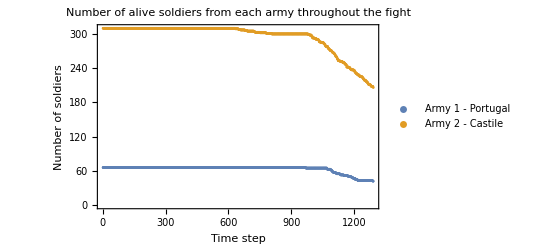

```mathematica
(*Graph section*)
ListPlot[{NofTroops1,NofTroops2},PlotLabel->"Number of alive soldiers from each army throughout the fight",
Frame->True,
FrameLabel->{"Time step", "Number of soldiers"},
PlotLegends->{"Army 1 - Portugal","Army 2 - Castile"}]
```

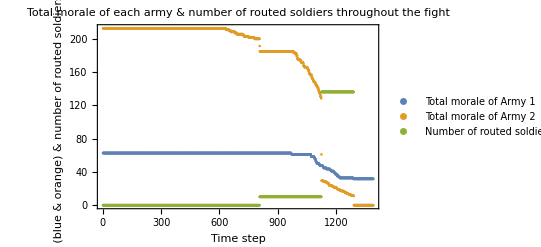

```mathematica
ListPlot[{TotMorale1, TotMorale2, NofRouted}, PlotLegends->{"Total morale of Army 1","Total morale of Army 2","Number of routed soldiers"},Frame->True,
FrameLabel->{"Time step", "Morale (blue & orange) & number of routed soldiers (green)"},PlotLabel->"Total morale of each army & number of routed soldiers throughout the fight"]
```

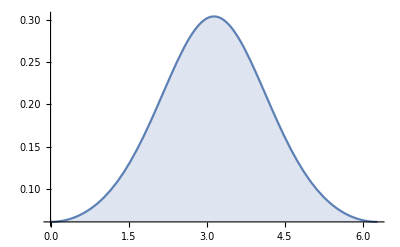

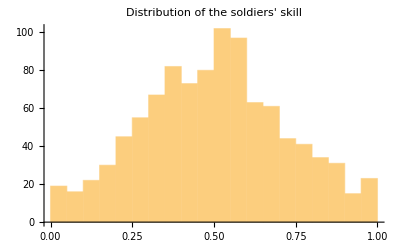

```mathematica
Plot[PDF[VonMisesDistribution[Pi,0.8],x]//Evaluate,{x,0,2*Pi},PlotRange->All,Filling->Axis]
moraletable=RandomVariate[VonMisesDistribution[Pi,0.8], 1000]/(2*Pi);
Histogram[moraletable, 25,PlotLabel->"Distribution of the soldiers' skill"]
```

```mathematica
(* piece of code that saves the last run simulation into 10 gifs (simulation is in 10 parts) *)
(*DO NOT RUN - IT TAKES 2 HOURS TO COMPLETE*)
```

```mathematica
Print[Now]

division=10;
part=Floor[Nsteps/division];
limit=Table[part*b,{b,0,division-1}];
AppendTo[limit,Nsteps];

For[a=1,a<=division,a++,
anim=Table[Image[ListPlot[{ Army2Rout[[m]],Army1Infantry[[m]],Army1Lances[[m]],Army1Bowmen[[m]],Army2Infantry[[m]],Army2Lances[[m]],Army2Cavalry[[m]],Army2Bowmen[[m]]},Prolog->Inset[ImageMap],PlotRange->PlotRangee,PlotMarkers->{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},GridLines->Automatic,PlotLabel->"Animation of Soldiers' Movement", ImageSize->Full]],{m,limit[[a]]+1,limit[[a+1]],1}];

Export["battle_sim_"<>ToString[a]<>".gif",anim];

Print["Part ", a, " done ", Now];

Clear[anim];
];

Print["THE END ", Now]
```

Mon 24 Apr 2023 15:22:44GMT+1

Part 1 done Mon 24 Apr 2023 15:24:24GMT+1

Part 2 done Mon 24 Apr 2023 15:26:00GMT+1

Part 3 done Mon 24 Apr 2023 15:28:03GMT+1

Part 4 done Mon 24 Apr 2023 15:29:28GMT+1

Part 5 done Mon 24 Apr 2023 15:30:46GMT+1

Part 6 done Mon 24 Apr 2023 15:32:03GMT+1

Part 7 done Mon 24 Apr 2023 15:33:21GMT+1

Part 8 done Mon 24 Apr 2023 15:34:37GMT+1

Part 9 done Mon 24 Apr 2023 15:35:57GMT+1

Part 10 done Mon 24 Apr 2023 15:37:21GMT+1

THE END Mon 24 Apr 2023 15:37:21GMT+1